# Optimization of the Irreversible Stirling cycle for variable (θ_min, θ_max)

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory["C:\\Users\\DirName"]
```

```mathematica
dir = Directory[];
```

```mathematica
<<MaTeX`
```

## Definitions

```mathematica
Wqs[ν_,χ_]:=(1-ν)/2 Log[χ];
A[χ_]:=(1/(√χ)-1)^2;
w[ν_,χ_]:=(-Wqs[ν,χ])/(A[χ]*(1+√ν)^2);
tisoc[ν_,χ_]:=-1/(2χ)Log[ν];
σ[ν_,χ_]:=√(1+w[ν,χ]*tisoc[ν,χ]);
sAB[ν_,χ_]:=(1+σ[ν,χ])/(w[ν,χ]*(1+√ν));
sCD[ν_,χ_]:=√ν*sAB[ν,χ];
WAB[ν_,χ_]:=Log[χ]/2+A[χ]/sAB[ν,χ];
WCD[ν_,χ_]:=(-ν*Log[χ])/2+(ν*A[χ])/sCD[ν,χ];
P[ν_,χ_]:=-(WAB[ν,χ]+WCD[ν,χ])/(sAB[ν,χ]+sCD[ν,χ]+tisoc[ν,χ]);
η[ν_,χ_]:=1+WCD[ν,χ]/WAB[ν,χ];
ηC[ν_]:=1-ν;
ηCA[ν_]:=1-√ν;
```

```mathematica
tisocT[ν_,χ_,θmin_,θmax_]:=1/(2χ)Log[(1-θmin)/(ν-θmin)]+1/2 Log[(θmax-ν)/(θmax-1)];
σT[ν_,χ_,θmin_,θmax_]:=√(1+w[ν,χ]*tisocT[ν,χ,θmin,θmax]);
sABT[ν_,χ_,θmin_,θmax_]:=(1+σT[ν,χ,θmin,θmax])/(w[ν,χ]*(1+√ν));
sCDT[ν_,χ_,θmin_,θmax_]:=√ν*sABT[ν,χ,θmin,θmax];
WABT[ν_,χ_,θmin_,θmax_]:=Log[χ]/2+A[χ]/sABT[ν,χ,θmin,θmax];
WCDT[ν_,χ_,θmin_,θmax_]:=(-ν*Log[χ])/2+(ν*A[χ])/sCDT[ν,χ,θmin,θmax];
PT[ν_,χ_,θmin_,θmax_]:=-((WABT[ν,χ,θmin,θmax]+WCDT[ν,χ,θmin,θmax])/(sABT[ν,χ,θmin,θmax]+sCDT[ν,χ,θmin,θmax]+tisocT[ν,χ,θmin,θmax]));
pχoptT[ν_,θmin_,θmax_]:=FindMaximum[{PT[ν,χ,θmin,θmax],0<χ<1,θmin<ν<1},{χ,0.5}]
poptT[ν_,θmin_,θmax_]:=First[pχoptT[ν,θmin,θmax]]
χoptT[ν_,θmin_,θmax_]:=χ/.Last[pχoptT[ν,θmin,θmax]]
ηT[ν_,χ_,θmin_,θmax_]:=1+WCDT[ν,χ,θmin,θmax]/WABT[ν,χ,θmin,θmax];
ηoptT[ν_,θmin_,θmax_]:=ηT[ν,χoptT[ν,θmin,θmax],θmin,θmax];
```

```mathematica
LTicks[xm_,xM_,ΔxM_,Δxm_,n_]:=Join[Table[{x,NumberForm[x,{4,n}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

LTicksLegend[xm_,xM_,ΔxM_,Δxm_,n_]:=Join[Table[{x,NumberForm[x,{2,n}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

```mathematica
χsOpt=Import[dir<>"\\Data\\ChisOpt.dat"];
fχsOpt=Interpolation[χsOpt];
νopt:=ν/.Last[FindMaximum[{P[ν,fχsOpt[ν]],0<ν<1},{ν,0.08}]]
{νopt,fχsOpt[νopt],P[νopt,fχsOpt[νopt]]}
```

{0.0604619,0.507215,0.0413035}

```mathematica
νoptMmLIM = 0.06046194936863413;
χoptMmLIM = 0.5072150139857202;
```

## Figure 7

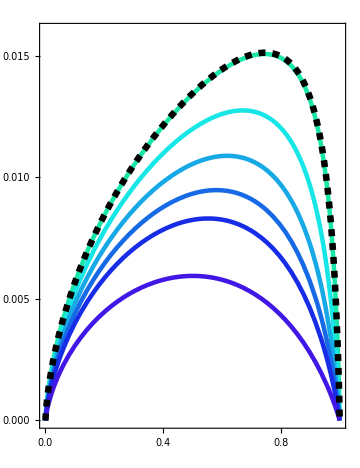

```mathematica
νp = 0.5;
θmaxp = 100;
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=0.016;Δym=0.001;ΔyM=0.005;
magnif = 2;
th = 0.009;

ColorFunc [c_]:=Hue[0.7*c+0.45*(1-c),0.9,0.9];
plotPvsχ[νp_,θmin_,θmax_,c_]:=Plot[PT[νp,χ,θmin,θmax],{χ,0,1},PlotStyle->{ColorFunc[c],Thickness[th]}];

α=-13;

min = 0.01;
max = 0.49999;
step = (max-min)/5;

tempMmVarP01=Show[Legended[Show[Table[plotPvsχ[νp,((max-min)*Exp[α*θmin])/(Exp[α*max]-Exp[α*min])+min-((max-min)*Exp[α*min])/(Exp[α*max]-Exp[α*min]),θmaxp,(θmin-min)/(max-min)],{θmin,min,max,step}]],LineLegend[Table[ColorFunc[(θmin-min)/(max-min)],{θmin,min,max,step}],Table[MaTeX[NumberForm[((max-min)*Exp[α*θmin])/(Exp[α*max]-Exp[α*min])+min-((max-min)*Exp[α*min])/(Exp[α*max]-Exp[α*min]),{5,3}],Magnification->0.8*magnif] ,{θmin,min,max,step}],LegendLabel->MaTeX["\\theta_{\\min}",Magnification->magnif],LegendMargins->{{10,0},{20,-5}}]],Plot[P[νp,χ],{χ,0,1},PlotRange->All,PlotStyle->{Black,Thickness[1.45*th],Dashed}],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->1.3,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,3],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\chi",Magnification->magnif],MaTeX["\\widetilde{\\mathcal{P}}(\\nu=0.5,\\chi;\\,\\theta_{\\min},\\theta_{\\max}\\to\\infty)",Magnification->1*magnif]},Frame->True,ImageSize->Medium]
```

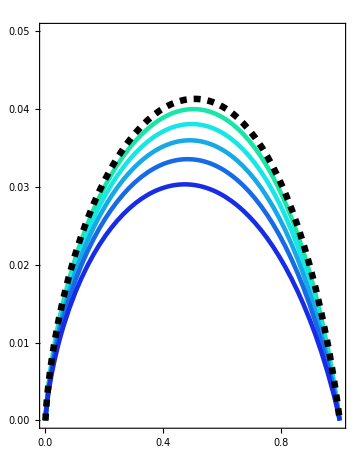

```mathematica
νp = νoptMmLIM;
θmaxp = 100;
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=0.05;Δym=0.005;ΔyM=0.01;
magnif = 2;
th = 0.009;

min = 0.01;
max = νoptMmLIM;
step = (max-min)/5;

tempMmVarP02=Show[Legended[Show[Table[plotPvsχ[νp,((max-min)*Exp[α*θmin])/(Exp[α*max]-Exp[α*min])+min-((max-min)*Exp[α*min])/(Exp[α*max]-Exp[α*min]),θmaxp,(θmin-min)/(max-min)],{θmin,min,max,step}]],LineLegend[Table[ColorFunc[(θmin-min)/(max-min)],{θmin,min,max,step}],Table[MaTeX[NumberForm[((max-min)*Exp[α*θmin])/(Exp[α*max]-Exp[α*min])+min-((max-min)*Exp[α*min])/(Exp[α*max]-Exp[α*min]),{4,2}],Magnification->0.8*magnif] ,{θmin,min,max,step}],LegendLabel->MaTeX["\\theta_{\\min}",Magnification->magnif],LegendMargins->{{10,0},{20,-5}}]],Plot[P[νp,χ],{χ,0,1},PlotRange->All,PlotStyle->{Black,Thickness[1.45*th],Dashed}],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->1.3,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\chi",Magnification->magnif],MaTeX["\\widetilde{\\mathcal{P}}(\\nu=\\nu^*_{\\text{id}},\\chi;\\,\\theta_{\\min},\\theta_{\\max}\\to\\infty)",Magnification->1*magnif]},Frame->True,ImageSize->Medium]
```

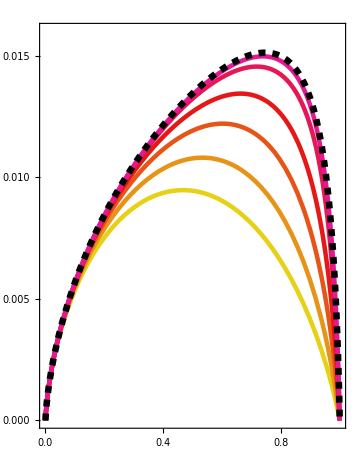

```mathematica
θminp=0;
νp = 0.5;
θmaxp = 100;
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=0.016;Δym=0.001;ΔyM=0.005;
magnif = 2;
th = 0.009;

ColorFunc [c_]:=Hue[-0.1*c+0.2*(1-c),0.9,0.9];
plotPvsχ[νp_,θmin_,θmax_,c_]:=Plot[PT[νp,χ,θmin,θmax],{χ,0,1},PlotStyle->{ColorFunc[c],Thickness[th]}];

α=1.125;

θmaxS={1.001,1.015,1.1,1.4,3,10};


min = 1.0001;
max = 10;
step = (max-min)/5;

tempMmVarP03=Show[Legended[Show[Table[plotPvsχ[νp,θminp,θmaxS[[j]],j/Length[θmaxS]],{j,1,Length[θmaxS],1}]],LineLegend[Table[ColorFunc[j/Length[θmaxS]],{j,1,Length[θmaxS],1}],Table[MaTeX[NumberForm[N[θmaxS[[j]]],{4,2}],Magnification->0.8*magnif] ,{j,1,Length[θmaxS],1}],LegendLabel->MaTeX["\\theta_{\\max}",Magnification->magnif],LegendMargins->{{10,0},{20,-5}}]],Plot[P[νp,χ],{χ,0,1},PlotRange->All,PlotStyle->{Black,Thickness[1.45*th],Dashed}],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->1.3,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,3],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\chi",Magnification->magnif],MaTeX["\\widetilde{\\mathcal{P}}(\\nu=0.5,\\chi;\\,\\theta_{\\min}\\to0,\\theta_{\\max})",Magnification->1*magnif]},Frame->True,ImageSize->Medium]
```

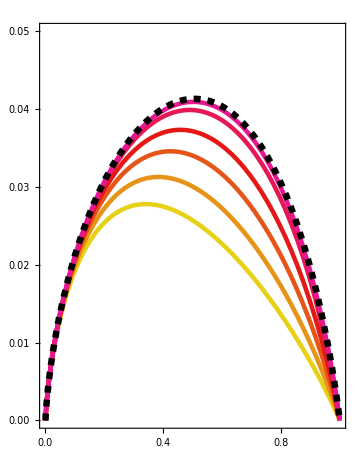

```mathematica
νp = νoptMmLIM;
θmaxp = 100;
xm=0;xM=1;Δxm=0.1;ΔxM=0.2;
ym=0;yM=0.05;Δym=0.005;ΔyM=0.01;
magnif = 2;
th = 0.009;

ColorFunc [c_]:=Hue[-0.1*c+0.2*(1-c),0.9,0.9];
plotPvsχ[νp_,θmin_,θmax_,c_]:=Plot[PT[νp,χ,θmin,θmax],{χ,0,1},PlotStyle->{ColorFunc[c],Thickness[th]}];



min = 1.0001;
max = 10;
step = (max-min)/5;

tempMmVarP04=Show[Legended[Show[Table[plotPvsχ[νp,θminp,θmaxS[[j]],j/Length[θmaxS]],{j,1,Length[θmaxS],1}]],LineLegend[Table[ColorFunc[j/Length[θmaxS]],{j,1,Length[θmaxS],1}],Table[MaTeX[NumberForm[N[θmaxS[[j]]],{4,2}],Magnification->0.8*magnif] ,{j,1,Length[θmaxS],1}],LegendLabel->MaTeX["\\theta_{\\max}",Magnification->magnif],LegendMargins->{{10,0},{20,-5}}]],Plot[P[νp,χ],{χ,0,1},PlotRange->All,PlotStyle->{Black,Thickness[1.45*th],Dashed}],PlotRange->{{xm,xM},{ym,yM}},AspectRatio->1.3,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,2],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True,PlotRangePadding->None,
LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->True,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\chi",Magnification->magnif],MaTeX["\\widetilde{\\mathcal{P}}(\\nu=\\nu^*_{\\text{id}},\\chi;\\,\\theta_{\\min}\\to0,\\theta_{\\max})",Magnification->1*magnif]},Frame->True,ImageSize->Medium]
```

## Figure 8. Density plots for variable θ_min, θ_max

```mathematica
L=50; 
am=0.0001;
bm = 0.4;
aM = 1.15;
bM = 1.5;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);
TableVariableLimTemps1=Flatten[Table[{θmin,θmax,ν,χ,PT[ν,χ,θmin,θmax],ηT[ν,χ,θmin,θmax]}/.Last[FindMaximum[{PT[ν,χ,θmin,θmax],θmin<ν<1,0<χ<1},{{ν,(θmin+1)/2},{χ,0.5}}]],{θmin,am,bm,δm},{θmax,aM,bM,δM}],1];
```

```mathematica
L=50; 
am=0.0001;
bm = 0.4;
aM = 1.5;
bM = 2.5;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);
TableVariableLimTemps2=Flatten[Table[{θmin,θmax,ν,χ,PT[ν,χ,θmin,θmax],ηT[ν,χ,θmin,θmax]}/.Last[FindMaximum[{PT[ν,χ,θmin,θmax],θmin<ν<1,0<χ<1},{{ν,(θmin+1)/2},{χ,0.5}}]],{θmin,am,bm,δm},{θmax,aM,bM,δM}],1];
```

```mathematica
TableVariableLimTemps = Join[TableVariableLimTemps1,TableVariableLimTemps2];
```

```mathematica
Export[dir<>"\\Data\\TableVariableLimTemps.dat",TableVariableLimTemps,"Table"];
```

```mathematica
TableVariableLimTemps = Import[dir<>"\\Data\\TableVariableLimTemps.dat"];
```

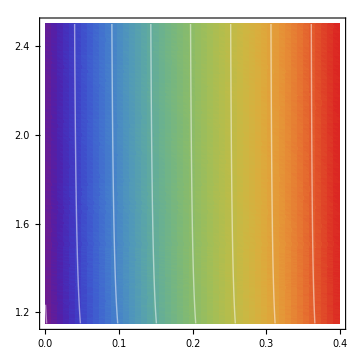

```mathematica
xm=0;xM=0.4;Δxm=0.025;ΔxM=0.1;
ym=1.2;yM=2.5;Δym=0.05;ΔyM=0.4;
max=0.42;min=0;step=0.1;Colors="Rainbow";
magnif = 2;
L = Length[TableVariableLimTemps];
tempMmVarDP01=Show[ListDensityPlot[Table[TableVariableLimTemps[[i]][[{1,2,3}]],{i,1,L}],InterpolationOrder->3,PlotRange->All,PlotRangePadding->None,ColorFunction->Colors,PlotLegends->BarLegend[{Colors,{min,max}},Ticks->LTicksLegend[min,max,step,step/4,1],LegendMarkerSize->250,LegendLabel->MaTeX["\\nu^{*}",Magnification->magnif],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\theta_{\\min}",Magnification->magnif],MaTeX["\\theta_{\\max}",Magnification->magnif]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True],Graphics[ListContourPlot[Table[TableVariableLimTemps[[i]][[{1,2,3}]],{i,1,L}],PlotRange->All,Contours->Table[x,{x,min,max,step/2}],ContourShading->False,ContourStyle->White]],PlotRange->{{xm,xM},{1.15,yM}}]
```

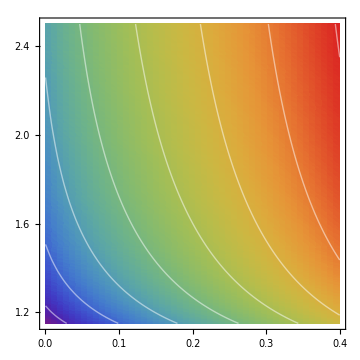

```mathematica
xm=0;xM=0.4;Δxm=0.025;ΔxM=0.1;
ym=1.2;yM=2.5;Δym=0.05;ΔyM=0.4;
max=0.6;min=0.4;step=0.04;Colors="Rainbow";
magnif = 2;

tempMmVarDP02=Show[ListDensityPlot[Table[TableVariableLimTemps[[i]][[{1,2,4}]],{i,1,L}],InterpolationOrder->3,PlotRange->All,PlotRangePadding->None,ColorFunction->Colors,PlotLegends->BarLegend[{Colors,{min,max}},Ticks->LTicksLegend[min,max,step,step/4,2],LegendMarkerSize->250,LegendLabel->MaTeX["\\chi^{**}",Magnification->magnif],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\theta_{\\min}",Magnification->magnif],MaTeX["\\theta_{\\max}",Magnification->magnif]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True],Graphics[ListContourPlot[Table[TableVariableLimTemps[[i]][[{1,2,4}]],{i,1,L}],PlotRange->All,Contours->Table[x,{x,min,max,step/2}],ContourShading->False,ContourStyle->White]],PlotRange->{{xm,xM},{1.15,yM}}]
```

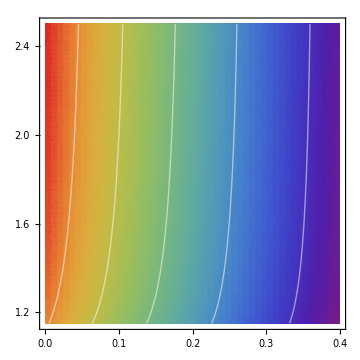

```mathematica
xm=0;xM=0.4;Δxm=0.025;ΔxM=0.1;
ym=1.2;yM=2.5;Δym=0.05;ΔyM=0.4;
max=0.04;min=0.01;step=0.005;Colors="Rainbow";
magnif = 2;

tempMmVarDP03=Show[ListDensityPlot[Table[TableVariableLimTemps[[i]][[{1,2,5}]],{i,1,L}],InterpolationOrder->3,PlotRange->All,PlotRangePadding->None,ColorFunction->Colors,PlotLegends->BarLegend[{Colors,{min,max}},Ticks->LTicksLegend[min,max,step,step/4,3],LegendMarkerSize->250,LegendLabel->MaTeX["\\widetilde{\\mathcal{P}}^{**}",Magnification->magnif],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\theta_{\\min}",Magnification->magnif],MaTeX["\\theta_{\\max}",Magnification->magnif]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True],Graphics[ListContourPlot[Table[TableVariableLimTemps[[i]][[{1,2,5}]],{i,1,L}],PlotRange->All,Contours->Table[x,{x,min,max,step}],ContourShading->False,ContourStyle->White]],PlotRange->{{xm,xM},{1.15,yM}}]
```

```mathematica
L=35; 
am=0.0001;
bm = 0.222;
aM = 1.15;
bM = 2.5;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);
TableEfficiencies1=Flatten[Table[{θmin,θmax,ν,ηT[ν,χ,θmin,θmax]}/.Last[FindMaximum[{PT[ν,χ,θmin,θmax],θmin<ν<1,0<χ<1},{{ν,(θmin+1)/2},{χ,0.5}}]],{θmin,am,bm,δm},{θmax,aM,bM,δM}],1];
```

```mathematica
L=35; 
am= 0.222;
bm =0.4;
aM = 1.15;
bM = 2.5;
δm = (bm-am)/(L-1);
δM = (bM-aM)/(L-1);
TableEfficiencies2=Flatten[Table[{θmin,θmax,ν,ηT[ν,χ,θmin,θmax]}/.Last[FindMaximum[{PT[ν,χ,θmin,θmax],θmin<ν<1,0<χ<1},{{ν,(θmin+1)/2},{χ,0.5}}]],{θmin,am,bm,δm},{θmax,aM,bM,δM}],1];
```

```mathematica
TableEfficienciesVariableLimTemps= Join[TableEfficiencies1,TableEfficiencies2];
```

```mathematica
Export[dir<>"\\Data\\TableEfficienciesVariableLimTemps.dat",TableEfficienciesVariableLimTemps,"Table"];
```

```mathematica
TableEfficienciesVariableLimTemps=Import[dir<>"\\Data\\TableEfficienciesVariableLimTemps.dat"];
```

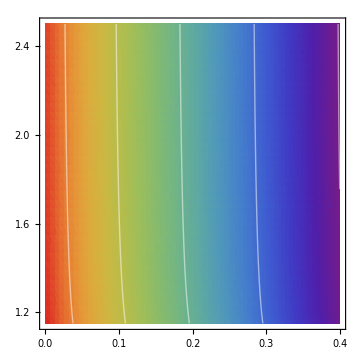

```mathematica
xm=0;xM=0.4;Δxm=0.025;ΔxM=0.1;
ym=1.2;yM=2.5;Δym=0.05;ΔyM=0.4;
max=0.9;min=0.4;step=0.1;Colors="Rainbow";
magnif = 2;
L1 = 35;
L2 = 70;

tempMmVarDP04=Show[ListDensityPlot[Table[{TableEfficienciesVariableLimTemps[[i]][[1]],TableEfficienciesVariableLimTemps[[i]][[2]],TableEfficienciesVariableLimTemps[[i]][[4]]},{i,1,L1*L2}],InterpolationOrder->3,PlotRange->All,PlotRangePadding->None,ColorFunction->Colors,PlotLegends->BarLegend[{Colors,{min,max}},Ticks->LTicksLegend[min,max,step,step/4,1],LegendMarkerSize->250,LegendLabel->MaTeX["\\tilde{\\eta}^{**}",Magnification->magnif],LegendMargins->{{-4,0},{35,0}}],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],RotateLabel->False,Axes->False,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameLabel->{MaTeX["\\theta_{\\min}",Magnification->magnif],MaTeX["\\theta_{\\max}",Magnification->magnif]},ImageSize->Medium,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym,1],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm,1],STicks[xm,xM,ΔxM,Δxm]}},PlotRangeClipping->True],Graphics[ListContourPlot[Table[{TableEfficienciesVariableLimTemps[[i]][[1]],TableEfficienciesVariableLimTemps[[i]][[2]],TableEfficienciesVariableLimTemps[[i]][[4]]},{i,1,L1*L2}],PlotRange->All,Contours->Table[x,{x,min,max,step}],ContourShading->False,ContourStyle->White]],PlotRange->{{xm,xM},{1.15,yM}}]
```